## Arabic Handwritten Characters Dataset

### Dataset available at https://www.kaggle.com/datasets/mloey1/ahcd1

```mathematica
NotebookDirectory[]
SetDirectory[NotebookDirectory[]]
```

/home/mk/Desktop/Arabic-Handwritten-Characters-Dataset/

/home/mk/Desktop/Arabic-Handwritten-Characters-Dataset

```mathematica
rawTrainLabels = Import["csvTrainLabel 13440x1.csv"];
rawTestLabels = Import["csvTestLabel 3360x1.csv"];
rawTrainImages = Import["csvTrainImages 13440x1024.csv"];
rawTestImages = Import["csvTestImages 3360x1024.csv"];
```

```mathematica
toImage[vec_]:= Image[Transpose@ArrayReshape[vec, {Sqrt[Length@vec],Sqrt[Length@vec]}]]
```

```mathematica
trainImages = Map[toImage,rawTrainImages];
testImages = Map[toImage,rawTestImages];
trainLabels = Flatten@rawTrainLabels;
testLabels = Flatten@rawTestLabels;
```

```mathematica
RandomSample[trainImages,50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
myLeNet = NetInitialize@NetChain[
{
ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],
ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[500],Ramp,LinearLayer[28],SoftmaxLayer[]
},
"Input"-> NetEncoder[{"Image",{32,32},ColorSpace->"Grayscale"}],
"Output"-> NetDecoder[{"Class",Alphabet["Arabic"] }]
]
```

NetChain[<>]

```mathematica
trainedNet = NetTrain[myLeNet,trainImages->trainLabels,
MaxTrainingRounds->10,
BatchSize->64]
```

NetChain[<>]

```mathematica
trainedNet[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{ت,ح,د,ج,و,ت,ض,خ,ر,ق}

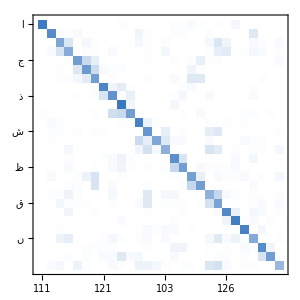
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[trainedNet,testImages->testLabels,"ConfusionMatrixPlot"]
```

```mathematica
NetMeasurements[trainedNet,testImages->testLabels,"Accuracy"]
```

0.742262